# MMA高级编程

## 一. 匿名函数

## 1.匿名函数(纯函数)

### 1.1 单参函数

```mathematica
g = # + #&
(* 1. 作用于单个值 *)
g[4]

(* 2. 作用于一个列表 *)
ls = {1, 2, 3};
g[ls]


h = ##&
h[3, 4]
```

#1+#1&

8

{2,4,6}

##1&

Sequence[3,4]

### 1.2 多参数函数

```mathematica
f = #1+#2&
f[1, 2]
```

#1+#2&

3

### 1.3 抽象函数

```mathematica
{#, #} & /@ {a, b, c, d}
```

{{a,a},{b,b},{c,c},{d,d}}

### 1.4 使用Function函数

```mathematica
Function[x, x^2][5]
```

25

```mathematica
Function[{x, y}, x+y][4, 2]
```

6

## 2. 背景知识补充

### 2.1 头部

什么是 头部 ？
实际上就是一个表达式的数据类型，比如 List, Integer, Float 等； 我们自定义的函数可以看作是一个 头部，所以才有了所谓的 Head 函数

具体写法如下： 主要就是一个抽象的单形参函数 f 的使用

```mathematica
Clear[f]
(* 用 f 替换头部 *)
expr = {a, b, c, d};
Apply[f, expr]

(* 检验头部 *)
expr//Head
Apply[f, expr]//Head
```

f[a,b,c,d]

List

f

### 2.2 常规的替换表头

比如把一个“列表”List的表头替换成Plus，我们就可以对”列表“中的元素求和了

Applypaclet:ref/Apply 可用于任何头部，而不仅仅是 Listpaclet:ref/List

```mathematica
Clear[g]
Apply[Plus, {1, 2, 3}]

Apply[Plus, g[x,y,z]]
```

6

x+y+z

### 2.3 一个抽象的头部

注：SlotSequence (##)(插符序列)

```mathematica
abstrcthead = Table[a[i, j], ##]&;

Apply[abstrcthead, {{i, 1, 3}, {j, 1, 2}}]//MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2]
a[3,1] | a[3,2])

## 3. 常见的简写

### 3.1 Map: 简写形式/@ (单个函数形参)

Map[f, expr] 或 f/@expr: 将 f 应用到 expr 中第一层的每个元素.

```mathematica
Clear[f, g]
(* 1.标准形式 *)
Map[f, {a, b, c}]

(* 2.简写形式 *)
g/@{a, b, c, d}

(* 注：这里的Map能够作用在列表上是应为Map默认作用在第一层 *)
```

{f[a],f[b],f[c]}

{g[a],g[b],g[c],g[d]}

```mathematica
f = {#, #}&;
(* 1.作用一个单个形参 *)
Map[f, 1]
f/@1

(* 2.作用单个形参列表 *)
Map[f, {1, 2}]
f/@{1, 2}


g = {#, #2}&;
(* 错误的写法： Map[g, {{1, 2}, {3, 4}}] *)
```

1

1

{{1,1},{2,2}}

{{1,1},{2,2}}

多个参数必须使用 Apply

### 3.2 Apply: 简写形式@@（多个函数形参）

1. f@@expr 或 Apply[f,expr]: 用 f 替换 expr的头部. 
2. Apply[f]: 表示 Apply的运算符形式，它可以应用于表达式.
3. Apply[f,expr,levelspec]: 替换 expr 中使用 levelspec 指定的部分的头部.

```mathematica
Clear[f]
(* 1.标准形式 *)
Apply[f, {{a,b}, {c}, d}]

(* 2.简写形式 *)

(* 3.运算符形式 *)
Apply[f][{{a,b}, {c}, d}]
```

f[{a,b},{c},d]

f[{a,b},{c},d]

具体写法，主要举例了 f 为一个具体的三个形参的函数时的情况

```mathematica
Clear[x]
fun1 = #1 + #2 + #3 &;

Apply[fun1, {1, 2, x}]
fun1@@{1, 2, x}

(* 错误的写法： Apply[fun1, {{1, 2, x}, {3, 4, y}}]*)
```

3+x

3+x

如果要作用于一个多参数组成的列表，就需要使用层这个概念了

### 3.3 操作的层的概念

为什么我们需要层的概念 -> 为了解决函数作用于列表的时候告诉程序：
1.列表整体是一个参数
2.列表中的元素为各个参数（传入多个复合函数形参的参数个数）

表达式所带的“层”对应于需要提取部分的索引号. 像 Map 这样的函数可以在指定的层进行操作。

跨越的大括号对数 = 层数

#### 3.3.1 Map 默认在第一层操作

```mathematica
Clear[f]
Map[f, {{a, b}, {c, d}}]

(*这个里面的整体元素就是 {a, b}, {c, d}*)
```

{f[{a,b}],f[{c,d}]}

#### 3.3.2 让Map 在第二层操作

```mathematica
Map[f, {{a, b}, {c, d}}, {2}]
```

{{f[a],f[b]},{f[c],f[d]}}

#### 3.3.3 Apply 默认在第零层操作

也就是直接把列表中的所有元素作为形参，作用得到一个一维的表达式

```mathematica
Apply[f, {{a,b,c}, {d,e}}]
```

f[{a,b,c},{d,e}]

#### 3.3.4 @@@ 是指“在第一层应用

也就是把列表中的每一个元素作为函数每一次作用的形参，作用得到的维度等于列表的维度

```mathematica
Apply[f, {{a,b,c}, {d,e}}, {1}]
```

{f[a,b,c],f[d,e]}

#### 3.3.5 @ 是指普通函数应用

```mathematica
f@x
```

f[x]

### 3.4 解决多参数匿名函数作用在列表上的问题

此时一般不能够用简写的形式， 但是Apply有一个@@@的简写

```mathematica
g = # + #2 + #3&;

g@@{1, 2, 3}
Apply[g, {1, 2, 3}]

Apply[g, {{1, 2, 3}, {4, 5, 6}}, {1}]
g@@@{{1, 2, 3}, {4, 5, 6}}
```

6

6

{6,15}

{6,15}

### 3.5 同时作用在多层

```mathematica
(* 解释：这里是先作用在第0层，然后再作用到得到结果的第1层 *)

(* 检验 *)
"作用在第0层后得到：" Apply[f, {{a,b,c}, {d,e}}]//ToString
"对上面的结果作用在第1层后得到：" Apply[f, Apply[f, {{a,b,c}, {d,e}}], {1}]
"最终的结果："Apply[f, {{a,b,c}, {d,e}}, {0, 1}]
```

作用在第0层后得到： f[{a, b, c}, {d, e}]

对上面的结果作用在第1层后得到： f[f[a,b,c],f[d,e]]

最终的结果： f[f[a,b,c],f[d,e]]

#### 3.5.1 向下应用至层 2 (层 0 除外)

```mathematica
Apply[f, {{{{{a}}}}}, 2]
```

{f[f[{{a}}]]}

#### 3.5.2 在层 0 至 2 应用

```mathematica
Apply[f, {{{{{a}}}}}, {0,2}]
```

f[f[f[{{a}}]]]

#### 3.5.3 在所有层应用，从层 1 开始

```mathematica
Apply[f, {{{{{a}}}}}, Infinity]
```

{f[f[f[f[a]]]]}

#### 3.5.4 从层0开始应用到所有层

```mathematica
Apply[f, {{{{{a}}}}}, {0, Infinity}]
```

f[f[f[f[f[a]]]]]

### 3.4 多个函数复合的运算次序

```mathematica
#1+#1&/@Plus[#1, #2]&@@{1, 2}
```

3

## 4. 一切/随处 皆可匿名

也就是说，无论在什么地方你都可以使用匿名函数

注意：匿名函数多个参数时：使用[]包括。

### 4.1 匿名函数使用方法

```mathematica
f[x_, y_] := x+y;
f[1, 2]

#+#2&[1, 2]

(*必须使用括号括起来表明是一个函数*)
(#+#2&)[1, 2]
```

3

3

3

### 4.2 使用示例

```mathematica
Rectangle[{0, 0}, {#, #2}] & @@ {2438, 1219}

(* 相比于这个直接命令方式要好：Rectangle[{0, 0}, {2438, 1219}]*)
```

Rectangle[{0,0},{2438,1219}]

```mathematica
Line[{{0, #}, {2438, #}} &[490]]

(* 相比于这个命令好：Line[{{0, 490}, {2438, 490}}] *)
```

Line[{{0,490},{2438,490}}]

```mathematica
Nest[Lighter, Red, 3]
```

RGBColor[1, Rational[19, 27], Rational[19, 27]]

```mathematica
Table[i^j, ##]& @@{{i,3}, {j,4}}//MatrixForm
```

(1 | 1 | 1 | 1
2 | 4 | 8 | 16
3 | 9 | 27 | 81)

### 一个循环与判断的例子

```mathematica
list = {1, 2, 3, 4, 5};
l = {};
For[i=1, i<7, i++, 
	If[i>2, AppendTo[l, i]]
]

l
```

{3,4,5,6}

```mathematica
list = {1, 2, 3, 4, 5};
l = Select[list, # > 2 &]
```

{3,4,5}

### 4.3 警告

自己写的程序不要过度的简化，防止自己以后都看不懂

不要一时简写一时爽，一直简写一直爽

```mathematica
myPrimeSum2 = Plus@@Prime/@Range[PrimePi[#]]&;


(* 尽量写成这种简洁的形式 *)
myPrimeSum2=Function[n, 
	Apply[Plus, 
		Map[
			Prime, Range[PrimePi[n]]
		]
	]
];
```

也尽量不要写下面这种代码

```mathematica
Narcissistic[n_] :=
  Reap[Scan[Module[{count = Join @@ ConstantArray @@@ #},
       Scan[
        If[(Sort@Tally@IntegerDigits[#^n .count] == 
            Sort@ Thread[{#, count}]), Sow[#^n .count]] &, 
        Fold[Function[{digitlist, num}, 
          Flatten[Function[e, 
             Join[e, #] & /@ 
              Subsets[Complement[Range[0, 9], e], {num}]] /@ 
            digitlist, 1]], {{}}, #[[All, 2]]]]
       ] &, Sort /@ Tally /@ IntegerPartitions[n, n]]][[2, 1]];
Narcissistic[10] // AbsoluteTiming
```

{1.19225,{4679307774}}

## 5.关联

关联将把键符与其值相关联， （ 用 -> 输入 → ）

```mathematica
<|"a" -> x, "b" -> y|>
```

<|a→x,b→y|>

```mathematica
%//Head
```

Association

### 5.1 将关联应用于一个键给出对应的值

```mathematica
%["a"]
```

1

### 5.2 在纯函数中，#key 选出在关联中对应于”key”的值

```mathematica
{#b, 1+#b} & [<|"a"->x, "b" -> y |>]
```

{15,16}

```mathematica
{#a, 1+#a} & [<|"a"->x, "b" -> y |>]
```

{1,2}

## 6. SlotSequence (##)(插符序列)

### 6.1 ##表示提供给纯函数的完全的参数序列

## 是 ##1 的一个简短形式，指的是函数的所有参数

```mathematica
f[x, ##, y, ##]&[a, b, c, d]
```

f[x,a,b,c,d,y,a,b,c,d]

### 6.2 指定参数起始位置

```mathematica
f[x, ##2, y]&[a, b, c, d]
```

f[x,b,c,d,y]

### 6.3 将迭代列表插入到一个Table

```mathematica
Table[a[i, j], ##]&@@{{i, 3}, {j, 2}}//MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2]
a[3,1] | a[3,2])

### 6.4 对应于##的原对象是一个Sequence

```mathematica
##&[a, b, c, d]
```

Sequence[a,b,c,d]

## 二. 常用高级函数

## 1. Module

主要有两种用法：
1. Modulepaclet:ref/Module[{x,y,…}, expr]: 指定在 expr 中出现的符号 x、y、… 应被当作局部值.(且不会受到全局变量的影响)
2. Modulepaclet:ref/Module[{x=x_0,…}, expr]: 用来定义 x, … 的初始值.

```mathematica
x = 3
y = 4
```

3

4

```mathematica
Module[
	{x, y},  x = 1; y=2;
	res = x+y;
]

(* 不会受到全局变量的影响 *)
res
```

3

```mathematica
Module[
	{x1, y1},  x1 = 1; y1=2;
	res = x1 + y1;
]

(* 一旦出了Module之外，变量就被清除了 *)
res
x1
y1
```

3

x1

y1

## 2. With

用法解释：
Withpaclet:ref/With[{x=x_0,y=y_0,…},expr]: 指定在 expr 中出现的符号 x、y、… 应当由 x_0、y_0、… 替换.

备注：With 比 Module 快

### 2.1 常见使用方法

```mathematica
With[{x=7, y=z}, x^2+y]
```

49+z

### 2.2 Withpaclet:ref/With即便没有估值也可以工作

```mathematica
(* 一个简单的函数变自量符号替换 *)
With[{x=a}, (1+x^2)&]
```

1+a^2&

### 2.3 多次使用替换

```mathematica
With[{y=Sin[1.0]}, Sum[y^i, {i,0,10}]]
```

5.36323

## 3. 综合Module和With

### 3.1 速度比较

```mathematica
Timing[Do[Module[{x=5},x;], {10^5}]]

Timing[Do[With[{x = 5}, x;], {10^5}]]
```

{0.03125,Null}

{0.015625,Null}

### 3.2 区别

Blockpaclet:ref/Block 仅局部化值；它并不替代值. Modulepaclet:ref/Module 创建新符号

```mathematica
{
	Block[{x=5}, Hold[x]],
	With[{x=5}, Hold[x]],
	Module[{x=5}, Hold[x]]
}
```

{Hold[x],Hold[5],Hold[x$235478]}

## 4. Nest 函数

函数解释
Nest[f,expr,n]: 返回一个将 f 作用于 expr 上 n 次后得到的表达式.

```mathematica
Nest[g, x, 3]
```

g[g[g[3]]]

```mathematica
Clear[y]
f[x_] := x^2;

Nest[f, y+1, 2]
```

(1+y)^4

```mathematica
Nest[(1+#)^2&, 1, 3]

(1+(1+(1+1)^2)^2)^2

(* 计算过程：(1+1)^2 -> (1+(1+1)^2)^2 -> (1+(1+(1+1)^2)^2)^2 *)
```

676

676

## 5. 查看表达式的原始代码

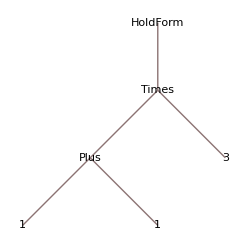

```mathematica
(1+1)*3//HoldForm//TreeForm
```